```mathematica
ClearAll["Global`*"]
```

```mathematica
data = Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/mathematica/NewRateFigures_Final/densitydata.csv"}],"csv"];
```

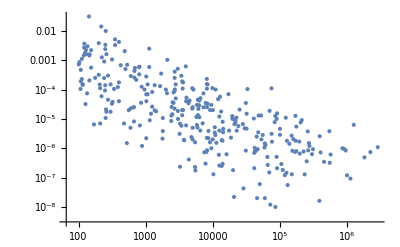

```mathematica
extractdatapos =Flatten[Position[data[[All,1]],x_/;x>100],1];
datalargebodied = data[[extractdatapos]];
ListLogLogPlot[datalargebodied]
```

```mathematica
LinearModelFit[Log@data,x,x]
```

FittedModel[-4.45983-0.776818 x]

```mathematica
LM=LinearModelFit[Log@datalargebodied,x,x]
```

FittedModel[-3.76403-0.850798 x]

```mathematica
(*Get the R-squared value*)
rSquared=LM["RSquared"]

(*Get the p-values for the coefficients*)
pValues=LM["ParameterPValues"]
```

0.533689

{2.42137×10^-18,2.73947×10^-54}

```mathematica
fStat[m_FittedModel]:={Mean[m["ANOVATableFStatistics"]],1-CDF[FRatioDistribution[Total[m["ANOVATableDegreesOfFreedom"][[1;;Length[m["ANOVATableFStatistics"]]]]],m["ANOVATableDegreesOfFreedom"][[-2]]],Mean[m["ANOVATableFStatistics"]]]};
```

```mathematica
fStat[LM]
```

{361.659,0.}

```mathematica
LM["ParameterConfidenceIntervals",ConfidenceLevel->.99]
```

{{-4.81303,-2.71503},{-0.966735,-0.73486}}

```mathematica
(*eqnC = ((λ)/(0.5*(k)))*R*C-(μ + σ*(1-R/(k)))*C/.{λ->λ[M]*(1+MODL),Y->Y[M]*(1+MODY),μ->0,ρ->ρ[M]*(1+MODR),σ->σ[M]*(1+MODS)};(*take σ*(1-R/k)=0 to take out starvation component*)
eqnR = α*R*(1-R/(k))-(((λ)/(Y))*(R/(0.5*(k)))+ρ)*C/.{λ->λ[M]*(1+MODL),Y->Y[M]*(1+MODY),μ->0,ρ->ρ[M]*(1+MODR),σ->σ[M]*(1+MODS)};*)

eqnC = λ*(R/(k/2+R))*C-( σ*(1-R/k)+μ)*C/.{λ->λ[M]*(1+MODL),Y->Y[M]*(1+MODY),μ->0,ρ->ρ[M]*(1+MODR),σ->σ[M]*(1+MODS)};(*take σ*(1-R/k)=0 to take out starvation component*)
eqnR = α*R*(1-R/(k))-( λ/Y*(R/(k/2+R))+ρ)*C/.{λ->λ[M]*(1+MODL),Y->Y[M]*(1+MODY),μ->0,ρ->ρ[M]*(1+MODR),σ->σ[M]*(1+MODS)};

LVSS = FullSimplify[Solve[{0==eqnC,0==eqnR},{C,R}]]
```

{{C→0,R→0},{C→0,R→k},{C→((1+MODY) α Y[M] (2 (1+MODL) (1+MODS) λ[M] σ[M] (-2 k (1+MODL) λ[M]+k (1+MODS) σ[M]+√(k^2 (4 (1+MODL)^2 λ[M]^2-4 (1+MODL) (1+MODS) λ[M] σ[M]+9 (1+MODS)^2 σ[M]^2)))+(1+MODR) (1+MODY) Y[M] ρ[M] (-4 k (1+MODL)^2 λ[M]^2+2 (1+MODL) λ[M] √(k^2 (4 (1+MODL)^2 λ[M]^2-4 (1+MODL) (1+MODS) λ[M] σ[M]+9 (1+MODS)^2 σ[M]^2))+(1+MODS) σ[M] (-3 k (1+MODS) σ[M]+√(k^2 (4 (1+MODL)^2 λ[M]^2-4 (1+MODL) (1+MODS) λ[M] σ[M]+9 (1+MODS)^2 σ[M]^2))))))/(4 (1+MODS)^2 σ[M]^2 (2 (1+MODR) (1+MODY) Y[M] ρ[M] ((1+MODL) λ[M]+(1+MODR) (1+MODY) Y[M] ρ[M])+(1+MODS) (2 (1+MODL) λ[M]+3 (1+MODR) (1+MODY) Y[M] ρ[M]) σ[M])),R→(-2 k λ[M]-2 k MODL λ[M]+k σ[M]+k MODS σ[M]+√(k^2 (8 (1+MODS)^2 σ[M]^2+(-2 (1+MODL) λ[M]+(1+MODS) σ[M])^2)))/(4 (1+MODS) σ[M])},{C→-(((1+MODY) α Y[M] (2 (1+MODL) (1+MODS) λ[M] σ[M] (2 k (1+MODL) λ[M]-k (1+MODS) σ[M]+√(k^2 (4 (1+MODL)^2 λ[M]^2-4 (1+MODL) (1+MODS) λ[M] σ[M]+9 (1+MODS)^2 σ[M]^2)))+(1+MODR) (1+MODY) Y[M] ρ[M] (4 k (1+MODL)^2 λ[M]^2+2 (1+MODL) λ[M] √(k^2 (4 (1+MODL)^2 λ[M]^2-4 (1+MODL) (1+MODS) λ[M] σ[M]+9 (1+MODS)^2 σ[M]^2))+(1+MODS) σ[M] (3 k (1+MODS) σ[M]+√(k^2 (4 (1+MODL)^2 λ[M]^2-4 (1+MODL) (1+MODS) λ[M] σ[M]+9 (1+MODS)^2 σ[M]^2))))))/(4 (1+MODS)^2 σ[M]^2 (2 (1+MODR) (1+MODY) Y[M] ρ[M] ((1+MODL) λ[M]+(1+MODR) (1+MODY) Y[M] ρ[M])+(1+MODS) (2 (1+MODL) λ[M]+3 (1+MODR) (1+MODY) Y[M] ρ[M]) σ[M]))),R→(-2 k λ[M]-2 k MODL λ[M]+k σ[M]+k MODS σ[M]-√(k^2 (8 (1+MODS)^2 σ[M]^2+(-2 (1+MODL) λ[M]+(1+MODS) σ[M])^2)))/(4 (1+MODS) σ[M])}}

```mathematica
Csol = C/.LVSS[[3]]
Rsol = R/.LVSS[[3]]
```

((1+MODY) α Y[M] (2 (1+MODL) (1+MODS) λ[M] σ[M] (-2 k (1+MODL) λ[M]+k (1+MODS) σ[M]+√(k^2 (4 (1+MODL)^2 λ[M]^2-4 (1+MODL) (1+MODS) λ[M] σ[M]+9 (1+MODS)^2 σ[M]^2)))+(1+MODR) (1+MODY) Y[M] ρ[M] (-4 k (1+MODL)^2 λ[M]^2+2 (1+MODL) λ[M] √(k^2 (4 (1+MODL)^2 λ[M]^2-4 (1+MODL) (1+MODS) λ[M] σ[M]+9 (1+MODS)^2 σ[M]^2))+(1+MODS) σ[M] (-3 k (1+MODS) σ[M]+√(k^2 (4 (1+MODL)^2 λ[M]^2-4 (1+MODL) (1+MODS) λ[M] σ[M]+9 (1+MODS)^2 σ[M]^2))))))/(4 (1+MODS)^2 σ[M]^2 (2 (1+MODR) (1+MODY) Y[M] ρ[M] ((1+MODL) λ[M]+(1+MODR) (1+MODY) Y[M] ρ[M])+(1+MODS) (2 (1+MODL) λ[M]+3 (1+MODR) (1+MODY) Y[M] ρ[M]) σ[M]))

(-2 k λ[M]-2 k MODL λ[M]+k σ[M]+k MODS σ[M]+√(k^2 (8 (1+MODS)^2 σ[M]^2+(-2 (1+MODL) λ[M]+(1+MODS) σ[M])^2)))/(4 (1+MODS) σ[M])

Analytical solution without the modifying terms

```mathematica
CsolSimp = FullSimplify[Expand[Csol/.{MODL->0,MODY->0,MODR->0,MODS->0}]]
RsolSimp=FullSimplify[Rsol/.{MODL->0,MODY->0,MODR->0,MODS->0}]
```

(α Y[M] (2 λ[M] σ[M] (-2 k λ[M]+k σ[M]+√(k^2 (4 λ[M]^2-4 λ[M] σ[M]+9 σ[M]^2)))+Y[M] ρ[M] (-4 k λ[M]^2+2 λ[M] √(k^2 (4 λ[M]^2-4 λ[M] σ[M]+9 σ[M]^2))+σ[M] (-3 k σ[M]+√(k^2 (4 λ[M]^2-4 λ[M] σ[M]+9 σ[M]^2))))))/(4 σ[M]^2 (2 Y[M] ρ[M] (λ[M]+Y[M] ρ[M])+(2 λ[M]+3 Y[M] ρ[M]) σ[M]))

(-2 k λ[M]+k σ[M]+√(k^2 (8 σ[M]^2+(-2 λ[M]+σ[M])^2)))/(4 σ[M])

```mathematica
CsolSimp/.{√(k^2 (4 λ[M]^2-4 λ[M] σ[M]+9 σ[M]^2))->A,ρ[M]->0}
```

(α Y[M] (A-2 k λ[M]+k σ[M]))/(4 σ[M]^2)

```mathematica
FullSimplify[(k √(8 σ[M]^2+(-2 λ[M]+σ[M])^2))/(k √(4 λ[M]^2-4 λ[M] σ[M]+9 σ[M]^2))]
```

1

```mathematica
jac =FullSimplify[{{ D[eqnR,R],D[eqnR,C]},{D[eqnC,R],D[eqnC,C]}}]/.{C->Csol,R->Rsol}
```

{{α-(α (-2 k λ[M]-2 k MODL λ[M]+k σ[M]+k MODS σ[M]+√(k^2 (8 (1+MODS)^2 σ[M]^2+(-2 (1+MODL) λ[M]+(1+MODS) σ[M])^2))))/(2 k (1+MODS) σ[M])-(k (1+MODL) α λ[M] (2 (1+MODL) (1+MODS) λ[M] σ[M] (-2 k (1+MODL) λ[M]+k (1+MODS) σ[M]+√(k^2 (4 (1+MODL)^2 λ[M]^2-4 (1+MODL) (1+MODS) λ[M] σ[M]+9 (1+MODS)^2 σ[M]^2)))+(1+MODR) (1+MODY) Y[M] ρ[M] (-4 k (1+MODL)^2 λ[M]^2+2 (1+MODL) λ[M] √(k^2 (4 (1+MODL)^2 λ[M]^2-4 (1+MODL) (1+MODS) λ[M] σ[M]+9 (1+MODS)^2 σ[M]^2))+(1+MODS) σ[M] (-3 k (1+MODS) σ[M]+√(k^2 (4 (1+MODL)^2 λ[M]^2-4 (1+MODL) (1+MODS) λ[M] σ[M]+9 (1+MODS)^2 σ[M]^2))))))/(2 (1+MODS)^2 σ[M]^2 (2 (1+MODR) (1+MODY) Y[M] ρ[M] ((1+MODL) λ[M]+(1+MODR) (1+MODY) Y[M] ρ[M])+(1+MODS) (2 (1+MODL) λ[M]+3 (1+MODR) (1+MODY) Y[M] ρ[M]) σ[M]) (k+(-2 k λ[M]-2 k MODL λ[M]+k σ[M]+k MODS σ[M]+√(k^2 (8 (1+MODS)^2 σ[M]^2+(-2 (1+MODL) λ[M]+(1+MODS) σ[M])^2)))/(2 (1+MODS) σ[M]))^2),-((1+MODR) ρ[M])-((1+MODL) λ[M] (-2 k λ[M]-2 k MODL λ[M]+k σ[M]+k MODS σ[M]+√(k^2 (8 (1+MODS)^2 σ[M]^2+(-2 (1+MODL) λ[M]+(1+MODS) σ[M])^2))))/(2 (1+MODS) (1+MODY) Y[M] σ[M] (k+(-2 k λ[M]-2 k MODL λ[M]+k σ[M]+k MODS σ[M]+√(k^2 (8 (1+MODS)^2 σ[M]^2+(-2 (1+MODL) λ[M]+(1+MODS) σ[M])^2)))/(2 (1+MODS) σ[M])))},{((1+MODY) α Y[M] (2 (1+MODL) (1+MODS) λ[M] σ[M] (-2 k (1+MODL) λ[M]+k (1+MODS) σ[M]+√(k^2 (4 (1+MODL)^2 λ[M]^2-4 (1+MODL) (1+MODS) λ[M] σ[M]+9 (1+MODS)^2 σ[M]^2)))+(1+MODR) (1+MODY) Y[M] ρ[M] (-4 k (1+MODL)^2 λ[M]^2+2 (1+MODL) λ[M] √(k^2 (4 (1+MODL)^2 λ[M]^2-4 (1+MODL) (1+MODS) λ[M] σ[M]+9 (1+MODS)^2 σ[M]^2))+(1+MODS) σ[M] (-3 k (1+MODS) σ[M]+√(k^2 (4 (1+MODL)^2 λ[M]^2-4 (1+MODL) (1+MODS) λ[M] σ[M]+9 (1+MODS)^2 σ[M]^2))))))/(4 k (1+MODS) σ[M] (2 (1+MODR) (1+MODY) Y[M] ρ[M] ((1+MODL) λ[M]+(1+MODR) (1+MODY) Y[M] ρ[M])+(1+MODS) (2 (1+MODL) λ[M]+3 (1+MODR) (1+MODY) Y[M] ρ[M]) σ[M]))+(k (1+MODL) (1+MODY) α Y[M] λ[M] (2 (1+MODL) (1+MODS) λ[M] σ[M] (-2 k (1+MODL) λ[M]+k (1+MODS) σ[M]+√(k^2 (4 (1+MODL)^2 λ[M]^2-4 (1+MODL) (1+MODS) λ[M] σ[M]+9 (1+MODS)^2 σ[M]^2)))+(1+MODR) (1+MODY) Y[M] ρ[M] (-4 k (1+MODL)^2 λ[M]^2+2 (1+MODL) λ[M] √(k^2 (4 (1+MODL)^2 λ[M]^2-4 (1+MODL) (1+MODS) λ[M] σ[M]+9 (1+MODS)^2 σ[M]^2))+(1+MODS) σ[M] (-3 k (1+MODS) σ[M]+√(k^2 (4 (1+MODL)^2 λ[M]^2-4 (1+MODL) (1+MODS) λ[M] σ[M]+9 (1+MODS)^2 σ[M]^2))))))/(2 (1+MODS)^2 σ[M]^2 (2 (1+MODR) (1+MODY) Y[M] ρ[M] ((1+MODL) λ[M]+(1+MODR) (1+MODY) Y[M] ρ[M])+(1+MODS) (2 (1+MODL) λ[M]+3 (1+MODR) (1+MODY) Y[M] ρ[M]) σ[M]) (k+(-2 k λ[M]-2 k MODL λ[M]+k σ[M]+k MODS σ[M]+√(k^2 (8 (1+MODS)^2 σ[M]^2+(-2 (1+MODL) λ[M]+(1+MODS) σ[M])^2)))/(2 (1+MODS) σ[M]))^2),((1+MODS) σ[M] (-k+(-2 k λ[M]-2 k MODL λ[M]+k σ[M]+k MODS σ[M]+√(k^2 (8 (1+MODS)^2 σ[M]^2+(-2 (1+MODL) λ[M]+(1+MODS) σ[M])^2)))/(4 (1+MODS) σ[M])))/k+((1+MODL) λ[M] (-2 k λ[M]-2 k MODL λ[M]+k σ[M]+k MODS σ[M]+√(k^2 (8 (1+MODS)^2 σ[M]^2+(-2 (1+MODL) λ[M]+(1+MODS) σ[M])^2))))/(2 (1+MODS) σ[M] (k+(-2 k λ[M]-2 k MODL λ[M]+k σ[M]+k MODS σ[M]+√(k^2 (8 (1+MODS)^2 σ[M]^2+(-2 (1+MODL) λ[M]+(1+MODS) σ[M])^2)))/(2 (1+MODS) σ[M])))}}

```mathematica
(* Parameters that go into the model *)
(* Those that rely on mass have been made into functions for better exploration *)

s=1;
B0=4.7*10^(-2);
Em=5774(*J/gram*);
Emprime =7000;
aprime =  B0/Emprime;
η=3/4;
γ=1.19;
ζ=1.00;
f0=0.0202;
mm0=0.383;
α=(*2.10*10^(-9)*)(9.45*10^(-9));
Ed=18200; (*J/g*)
k=(*5*)23000;
(*k=(*10*)23000/2;*)
ρ[M_]:=B0*M^(η)/(M*Ed);
Y[M_]:=M*Ed/BLam[M]; (*g individual/ g grass*)

a0 = 1.88*10^-8 ;(*sec grams^-b0*)
a1=1.45*10^-7;
a2=4.04*10^6;
b0=-0.56;
b1=-0.27;
b2=0.30;
μ[M_] := (a0*(Exp[a1*a2*M^(b1+b2)]-1)*M^(b0-b1-b2))/(a1*a2)   (* this is the consumer death rate*)


B0=4.7*10^(-2);(*W g^−0.75*)
Em=5774;(*J/gram*)
a = B0/Em;
m0[M_]:= (.0558*(1/1000)^.92*M^0.92)*1000;
ϵLam = 0.95;
τLam[M_]:= -Log[(1-ϵLam^(1/4))/(1 - (m0[M]/M)^(1/4))]*(4*M^(1/4))/a;
λ[M_]:=(Log[2]/τLam[M]) (*Fecundity = 2*) (* max consumer growth rate *)

(*STARVATION MORTALITY*)
ϵsig[M_] := (1-(f0*M^γ+mm0*M^ζ)/M);(*mortality from starvation state*)
τsig [M_]:=-M^(1/4)/aprime*Log[ϵsig[M]];(*time it takes to go from full to dead*)
σ[M_] := 1/τsig [M];(*starvation mortality rate)*)

E'=7000; (*J/g*)
a'=B0/E';
m[t_,M_]:=M*E^(-a'*t/(M^(1-η)))


(* Two version of Beta-lambda here. The first one doesn't take long to integrate numerically but gives slightly different results from the analytical version below *)
Bλ[M_]=Integrate[B0*m[t,M]^(η),{t,0,τLam[M]}];

BLam[M_]:=1/(3 a)ⅇ^(-(a τLam[M])/M^(1/4)) M^(1/4) (3 (-1+ⅇ^((a τLam[M])/M^(1/4))) m0[M]+M (-48 ⅇ^((3 a τLam[M])/(4 M^(1/4))) (-1+(m0[M]/M)^(1/4))-36 ⅇ^((a τLam[M])/(2 M^(1/4))) (-1+(m0[M]/M)^(1/4))^2-16 ⅇ^((a τLam[M])/(4 M^(1/4))) (-1+(m0[M]/M)^(1/4))^3+3 (-1+4 (m0[M]/M)^(1/4)-6 √(m0[M]/M)+4 (m0[M]/M)^(3/4))+ⅇ^((a τLam[M])/M^(1/4)) (-25+12 (m0[M]/M)^(1/4)+6 √(m0[M]/M)+4 (m0[M]/M)^(3/4)))+3 a ⅇ^((a τLam[M])/M^(1/4)) M^(3/4) τLam[M]);
```

Mass scaling of different components of consumer steady state

Consumer yield parameter  - insensitve to mass window

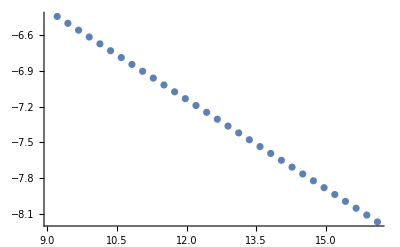

FittedModel[-4.13662-0.250236 x]

```mathematica
datatofit =Table[{Log[10^i],Log[Y[10^i]]},{i,4,7,0.1}];
ListPlot[datatofit]
LinearModelFit[datatofit,x,x]
```

Consumer growth rate - insensitve to mass window

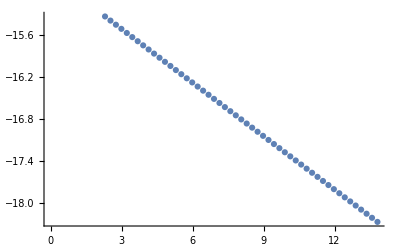

FittedModel[-14.7441-0.254912 x]

```mathematica
datatofit =Table[{Log[10^i],Log[λ[10^i]]},{i,1,6,0.1}];
ListPlot[datatofit]
LinearModelFit[datatofit,x,x]
```

Starvation rate - somewhat sensitive to Mass window (-0.3 for smaller masses, -0.37 for higher masses)

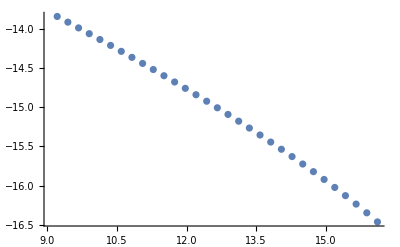

FittedModel[-10.3239-0.373815 x]

```mathematica
datatofit =Table[{Log[10^i],Log[σ[10^i]]},{i,4,7,0.1}];
ListPlot[datatofit]
LinearModelFit[datatofit,x,x]
```

Consumer steady state A parameter - somewhat sensitive to Mass window (-0.3 for smaller masses, -0.37 for higher masses)

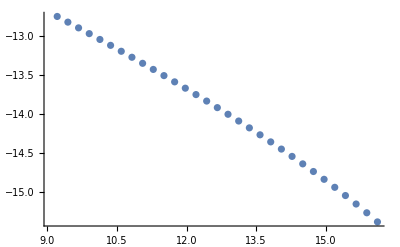

FittedModel[-9.21958-0.375203 x]

```mathematica
datatofit =Table[{Log[10^i],Log[√(4 λ[M]^2-4 λ[M] σ[M]+9 σ[M]^2)/.M->10^i]},{i,4,7,0.1}];
ListPlot[datatofit]
LinearModelFit[datatofit,x,x]
```

Consumer steady state A parameter - somewhat sensitive to Mass window (-0.3 for smaller masses, -0.37 for higher masses)

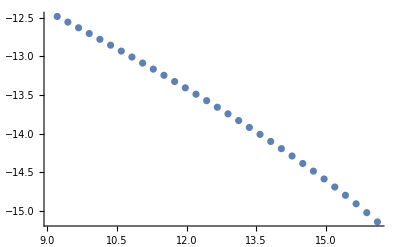

FittedModel[-8.91606-0.37849 x]

```mathematica
datatofit =Table[{Log[10^i],Log[( (A-2  λ[M]+σ[M])/.{A-> √(4 λ[M]^2-4 λ[M] σ[M]+9 σ[M]^2)})/.M->10^i]},{i,4,7,0.1}];
ListPlot[datatofit]
LinearModelFit[datatofit,x,x]
```

Full steady state - somewhat sensitive to Mass window (-0.93 for smaller masses, -0.8 for higher masses)

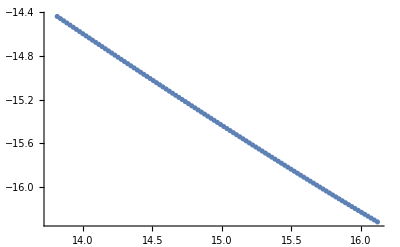

FittedModel[-3.13013-0.819708 x]

```mathematica
datatofit =Table[{Log[10^i],Log[(1/M)*(((α Y[M] (A-2 k λ[M]+k σ[M]))/(4 σ[M]^2))/.A->k*√(4 λ[M]^2-4 λ[M] σ[M]+9 σ[M]^2))/.M->10^i]},{i,6,7,0.01}];
ListPlot[datatofit]
LinearModelFit[datatofit,x,x]
```

```mathematica
LM=LinearModelFit[Log@data,x,x]
```

FittedModel[-4.45983-0.776818 x]

Ensure that ρ does not play a major role - the steady states overlap, so ρ can be effectively ignored!

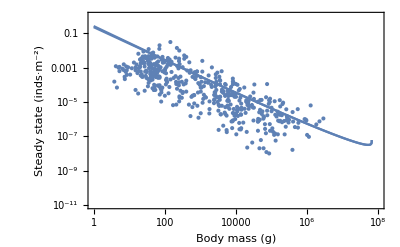

```mathematica
Show[{
ListLogLogPlot[data,PlotRange->{{1,10^8},{10^-11,1}},Frame->True,FrameLabel->{"Body mass (g)","Steady state (inds·m^-2)"},PlotRange->{10^-11,10^5}],
LogLogPlot[(1/M)*Csol/.{MODL->0,MODY->0,MODS->0,MODR->-1},{M,1,1*10^8},Frame->True],
LogLogPlot[(1/M)*Csol/.{MODL->0,MODY->0,MODS->0,MODR->0},{M,1,1*10^8},Frame->True]
}]
```

Manipulation of different parameters
MODL: modifies λ
ModY: modifies Y
ModS: modifies σ
ModR: modifies ρ

```mathematica
Manipulate[
Show[{
ListLogLogPlot[data,PlotRange->{{1,10^8},{10^-11,1}},Frame->True,FrameLabel->{"Body mass (g)","Steady state (inds·m^-2)"},PlotRange->{10^-11,10^5}],
LogLogPlot[(1/M)*Csol/.{MODL->modl,MODY->mody,MODS->mods,MODR->modr},{M,1,1*10^8},Frame->True],
LogLogPlot[Exp[-4.459834805724913]*x^-0.7768181657741381,{x,1,10^8},PlotStyle->Directive[Dashed]]
}],
{{modl,0},-1,1},
{{mody,0},-1,1},
{{mods,0},-1,1},
{{modr,0},-1,1}]
```

Plot RATES

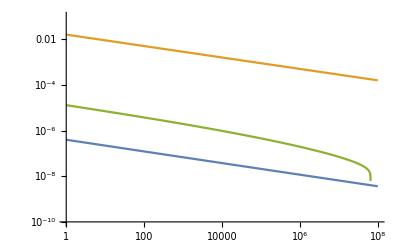

```mathematica
Show[{
LogLogPlot[λ[M],{M,1,10^8},PlotRange->{1*10^-10,0.1},PlotStyle->ColorData[97,1]]/.{MODL->0,MODY->0,MODS->0,MODR->0},
LogLogPlot[Y[M],{M,1,10^8},PlotStyle->ColorData[97,2]]/.{MODL->0,MODY->0,MODS->0,MODR->0},
LogLogPlot[σ[M],{M,1,10^8},PlotStyle->ColorData[97,3]]/.{MODL->0,MODY->0,MODS->0,MODR->0}
}]
```

```mathematica
D[λ[M],M]/.M->100
```

-3.12305×10^-10

```mathematica
k
```

23000

```mathematica
Remove[maxmod]
```

5.291*10^10 seconds = 1676 years
2.1164*10^7 seconds = 245 days = 0.67 years

```mathematica
Csol/.M->10
```

(0.426741 (1+MODY) (3.10902×10^-12 (1+MODL) (1+MODS) (-0.0101308 (1+MODL)+0.162344 (1+MODS)+23000 √(1.94013×10^-13 (1+MODL)^2-6.21803×10^-12 (1+MODL) (1+MODS)+4.48392×10^-10 (1+MODS)^2))+1.30688×10^-8 (1+MODR) (-4.46229×10^-9 (1+MODL)^2+0.0101308 (1+MODL) √(1.94013×10^-13 (1+MODL)^2-6.21803×10^-12 (1+MODL) (1+MODS)+4.48392×10^-10 (1+MODS)^2)+7.05843×10^-6 (1+MODS) (-0.487031 (1+MODS)+23000 √(1.94013×10^-13 (1+MODL)^2-6.21803×10^-12 (1+MODL) (1+MODS)+4.48392×10^-10 (1+MODS)^2))) (1+MODY)))/((1+MODS)^2 (2.61375×10^-8 (1+MODR) (1+MODY) (2.20234×10^-7 (1+MODL)+1.30688×10^-8 (1+MODR) (1+MODY))+7.05843×10^-6 (1+MODS) (4.40469×10^-7 (1+MODL)+3.92063×10^-8 (1+MODR) (1+MODY))))

```mathematica
10^1
```

10

```mathematica
Table[10^i,{i,{0}}]
```

{1}

How does the intercept vary across parameters?

```mathematica
massvec = Table[10^i,{i,{0}}];
decon={{Show[{LogPlot[Evaluate@Table[(1/M)*Csol/.{MODR->0,MODY->0,MODS->0,M->i},{i,massvec}],{MODL,-1,1},PlotRange->{0.01,10},PlotStyle->Black,FrameLabel->{"",""},Ticks->{None,Automatic},Frame->{False,True,True,True}],
Graphics[Text[Style["λ_C^max",Large],{0.68,Log@0.025}]]
}] (*Table[ColorData["BlueGreenYellow",i],{i,0,1,1/(Length[massvec]-1)}]*)
},(*,FrameLabel->{"Proportion change","Steady state (inds·m^-2)"}*)
{Show[{LogPlot[Evaluate@Table[(1/M)*Csol/.{MODR->0,MODL->0,MODS->0,M->i},{i,massvec}],{MODY,-1,1},PlotRange->{0.01,10},FrameLabel->{"","Steady state intercept (inds·m^-2)"},PlotStyle->Black,Ticks->{None,Automatic},Frame->{False,True,True,True}],
Graphics[Text[Style["Y_C",Large],{0.68,Log@0.025}]]
}]
},
{Show[{LogPlot[Evaluate@Table[(1/M)*Csol/.{MODR->0,MODL->0,MODY->0,M->i},{i,massvec}],{MODS,-1,1},PlotRange->{0.01,10},FrameLabel->{"Proportion change χ",""},PlotStyle->Black,Frame->True],
Graphics[Text[Style["σ^max",Large],{0.68,Log@0.025}]]
}]
}};
InterceptModPlot=ResourceFunction["PlotGrid"][decon,Spacings->{0,0}]
```

-Graphics-

```mathematica
Export[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2021_TaranWebs/figures/fig_intmod.pdf"}],InterceptModPlot,"PDF"]
```

/Users/jdyeakel/Dropbox/PostDoc/2021_TaranWebs/figures/fig_intmod.pdf

How does the slope vary across parameters at large body masses?

```mathematica
minmass = 10^6; (*10^4*)
maxmass = 10^7;
massmult = 10^4; (*10^3*)
decon={{Show[{Plot[(Log[((1/M)*Csol)/.{MODR->0,MODY->0,MODS->0,M->maxmass}] -Log[((1/M)*Csol)/.{MODR->0,MODY->0,MODS->0,M->minmass}]) /(Log[maxmass ]-Log[minmass]),{MODL,-0.99,1},PlotRange->{-0.95,-0.55},PlotStyle->Black,FrameLabel->{"",""},Ticks->{None,Automatic},Frame->{False,True,True,True}],
Graphics[Text[Style["λ_C^max",Large],{0.68,-0.9}]]
}]
},(*,FrameLabel->{"Proportion change","Steady state (inds·m^-2)"}*)
{Show[{Plot[(Log[((1/M)*Csol)/.{MODR->0,MODL->0,MODS->0,M->maxmass}]-Log[((1/M)*Csol)/.{MODR->0,MODL->0,MODS->0,M->minmass}])/(Log[maxmass] -Log[ minmass]),{MODY,-0.99,1},PlotRange->{-0.95,-0.55},FrameLabel->{"","Slope log(inds/m^2)/log(g/ind)"},PlotStyle->Black,Ticks->{None,Automatic},Frame->{False,True,True,True}],
Graphics[Text[Style["Y_C",Large],{0.68,-0.9}]]
}]
},
{Show[{Plot[(Log[((1/M)*Csol)/.{MODR->0,MODL->0,MODY->0,M->maxmass}]-Log[((1/M)*Csol)/.{MODR->0,MODL->0,MODY->0,M->minmass}])/(Log[maxmass] -Log[ minmass]),{MODS,-0.99,1},PlotRange->{-0.95,-0.55},FrameLabel->{"Proportion change χ",""},PlotStyle->Black,Frame->True],
Graphics[Text[Style["σ^max",Large],{0.68,-0.9}]]
}]
}};
SlopeModPlot=ResourceFunction["PlotGrid"][decon,Spacings->{0,2}]
```

-Graphics-

```mathematica
Export[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2021_TaranWebs/figures/fig_slopemod.pdf"}],SlopeModPlot,"PDF"]
```

/Users/jdyeakel/Dropbox/PostDoc/2021_TaranWebs/figures/fig_slopemod.pdf

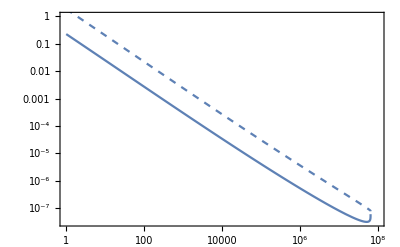

```mathematica
Show[{
LogLogPlot[(1/M)*Csol/.{MODL->0,MODY->0,MODS->0,MODR->0},{M,1,1*10^8},Frame->True],
LogLogPlot[(1/M)*Csol/.{MODL->0,MODY->0,MODS->-0.9,MODR->0},{M,1,1*10^8},Frame->True,PlotStyle->Dashed]
}]
```

```mathematica
StarvePlots=ParallelTable[((1/M)*Csol/.{MODL->0,MODY->0,MODS->i,MODR->0})-((1/M)*Csol/.{MODL->0,MODY->0,MODS->0,MODR->0}),{i,-0.99,1,0.01}];
```

```mathematica
StarvePlotsRelative=ParallelTable[(((1/M)*Csol/.{MODL->0,MODY->0,MODS->i,MODR->0})-((1/M)*Csol/.{MODL->0,MODY->0,MODS->0,MODR->0}))/(((1/M)*Csol/.{MODL->0,MODY->0,MODS->0,MODR->0})),{i,-0.98,1,0.01}];
```

```mathematica
SteadyStateDiffPlot=
Show[{
LogLinearPlot[StarvePlots,{M,1,1*10^3},Frame->True,PlotRange->{-0.5,1},FrameLabel->{"Consumer body mass M_C (g)","Δ steady state inds·m^-2"},PlotStyle->"Rainbow",LabelStyle->Directive[FontSize->16],PlotLegends->BarLegend[{"Rainbow",{-1,1}},LegendLabel->"σ(1+χ)"]](*,
LogLinearPlot[((1/M)*Csol/.{MODL->0,MODY->-0.9,MODS->0,MODR->0})-((1/M)*Csol/.{MODL->0,MODY->0,MODS->0,MODR->0}),{M,1,1*10^7},PlotRange->All]*)
(*LogLinearPlot[((1/M)*Csol/.{MODL->0,MODY->-0.9,MODS->0,MODR->0})-((1/M)*Csol/.{MODL->0,MODY->0,MODS->0,MODR->0}),{M,1,1*10^7},PlotRange->All]*)
},ImageSize->500]
```

-Graphics-

```mathematica
Export[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2021_TaranWebs/figures/fig_starve.pdf"}],SteadyStateDiffPlot,"PDF"]
```

/Users/jdyeakel/Dropbox/PostDoc/2021_TaranWebs/figures/fig_starve.pdf

```mathematica
SteadyStateRelDiffPlot=
Show[{
LogLinearPlot[StarvePlotsRelative,{M,1,1*10^8},Frame->True,PlotRange->{-1,20},FrameLabel->{"Consumer body mass M_C (g)","Change in steady state ΔC_s^* (inds·m^-2)"},PlotStyle->"BlueGreenYellow",LabelStyle->Directive[FontSize->16],PlotLegends->BarLegend[{"BlueGreenYellow",{-1,1}},LegendLabel->"χ_s"]](*,
LogLinearPlot[((1/M)*Csol/.{MODL->0,MODY->-0.9,MODS->0,MODR->0})-((1/M)*Csol/.{MODL->0,MODY->0,MODS->0,MODR->0}),{M,1,1*10^7},PlotRange->All]*)
(*LogLinearPlot[((1/M)*Csol/.{MODL->0,MODY->-0.9,MODS->0,MODR->0})-((1/M)*Csol/.{MODL->0,MODY->0,MODS->0,MODR->0}),{M,1,1*10^7},PlotRange->All]*)
},ImageSize->500]
```

-Graphics-

```mathematica
Export[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2021_TaranWebs/figures/fig_starverelative.pdf"}],SteadyStateRelDiffPlot,"PDF"]
```

/Users/jdyeakel/Dropbox/PostDoc/2021_TaranWebs/figures/fig_starverelative.pdf